# Blatt 6

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
rawData={0,1400,10,1386,20,1130,30,1045,40,971,50,862,60,819,70,808,80,862,90,829,100,824,110,839,120,819,130,901,140,925,150,1044,160,1224}
```

{0,1400,10,1386,20,1130,30,1045,40,971,50,862,60,819,70,808,80,862,90,829,100,824,110,839,120,819,130,901,140,925,150,1044,160,1224}

```mathematica
(*rawData={155,182,5,135,128,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,136,8,20,214,7}*)
```

```mathematica
data=Partition[rawData,2]
```

{{0,1400},{10,1386},{20,1130},{30,1045},{40,971},{50,862},{60,819},{70,808},{80,862},{90,829},{100,824},{110,839},{120,819},{130,901},{140,925},{150,1044},{160,1224}}

```mathematica
data//TeXForm//CopyToClipboard
```

## Processed Data

```mathematica
processedData={#[[1]],#[[2]],N@Sqrt[#[[2]]]}&/@data
```

{{0,1400,37.4166},{10,1386,37.229},{20,1130,33.6155},{30,1045,32.3265},{40,971,31.1609},{50,862,29.3598},{60,819,28.6182},{70,808,28.4253},{80,862,29.3598},{90,829,28.7924},{100,824,28.7054},{110,839,28.9655},{120,819,28.6182},{130,901,30.0167},{140,925,30.4138},{150,1044,32.311},{160,1224,34.9857}}

```mathematica
veryProcessedData={#[[1]], N@Cos[#[[1]] Degree],#[[2]],#[[3]]}&/@processedData
```

{{0,1.,1400,37.4166},{10,0.984808,1386,37.229},{20,0.939693,1130,33.6155},{30,0.866025,1045,32.3265},{40,0.766044,971,31.1609},{50,0.642788,862,29.3598},{60,0.5,819,28.6182},{70,0.34202,808,28.4253},{80,0.173648,862,29.3598},{90,0.,829,28.7924},{100,-0.173648,824,28.7054},{110,-0.34202,839,28.9655},{120,-0.5,819,28.6182},{130,-0.642788,901,30.0167},{140,-0.766044,925,30.4138},{150,-0.866025,1044,32.311},{160,-0.939693,1224,34.9857}}

```mathematica
processedData//TeXForm//CopyToClipboard
```

## Legendre Fitting

```mathematica
LegendreP[0,x]
LegendreP[2,x]
LegendreP[4,x]
```

1

1/2 (-1+3 x^2)

1/8 (3-30 x^2+35 x^4)

```mathematica
f1[x_]:=1
f2[x_]:= 1/2 (-1+3 x^2)
f3[x_]:=1/8 (3-30 x^2+35 x^4)
```

```mathematica
xdata=N@Cos[# Degree]&/@processedData[[All,1]]
ydata=processedData[[All,2]]
yerror=processedData[[All,3]]
```

{1.,0.984808,0.939693,0.866025,0.766044,0.642788,0.5,0.34202,0.173648,0.,-0.173648,-0.34202,-0.5,-0.642788,-0.766044,-0.866025,-0.939693}

{1400,1386,1130,1045,971,862,819,808,862,829,824,839,819,901,925,1044,1224}

{37.4166,37.229,33.6155,32.3265,31.1609,29.3598,28.6182,28.4253,29.3598,28.7924,28.7054,28.9655,28.6182,30.0167,30.4138,32.311,34.9857}

```mathematica
flst={f1,f2,f3}
```

{f1,f2,f3}

```mathematica
MatrixForm[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

(0.0178849 | 0.0023014 | 0.000907646
0.0023014 | 0.00470132 | 0.00120236
0.000907646 | 0.00120236 | 0.00279581)

```mathematica
Δ=Det[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

1.95566×10^-7

```mathematica
sumf1f1=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f2=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f3=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f2=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f3=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf3f3=∑_(k=1)^Length[xdata] (f3[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf1=∑_(k=1)^Length[xdata] (ydata[[k]] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf2=∑_(k=1)^Length[xdata] (ydata[[k]] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf3=∑_(k=1)^Length[xdata] (ydata[[k]] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
```

```mathematica
Δ=Det[({{sumf1f1, sumf1f2, sumf1f3}, {sumf1f2, sumf2f2, sumf2f3}, {sumf1f3, sumf2f3, sumf3f3}})]
```

1.95566×10^-7

```mathematica
a1=(1/Δ) Det[({{sumyf1, sumf1f2, sumf1f3}, {sumyf2, sumf2f2, sumf2f3}, {sumyf3, sumf2f3, sumf3f3}})]
a2=(1/Δ)Det[({{sumf1f1, sumyf1, sumf1f3}, {sumf1f2, sumyf2, sumf2f3}, {sumf1f3, sumyf3, sumf3f3}})]
a3=(1/Δ)Det[({{sumf1f1, sumf1f2, sumyf1}, {sumf1f2, sumf2f2, sumyf2}, {sumf1f3, sumf2f3, sumyf3}})]
```

907.175

260.479

193.667

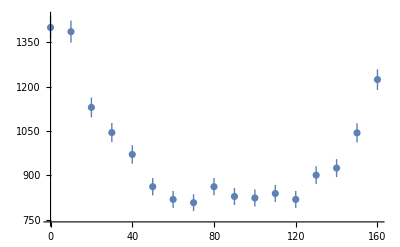

```mathematica
Show[ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData], Plot[93.3 f1[Cos[x Degree]]-10.6 f2[Cos[x Degree]]+164.4f3[Cos[x Degree]],{x,0,200}]]
```

```mathematica
FindFit[Transpose[{xdata, ydata}], a1f f1[x]+ a2f f2[x]+a3f f3[x],{a1f,a2f,a3f},x]
```

{a1f→97.4362,a2f→-4.59655,a3f→114.582}

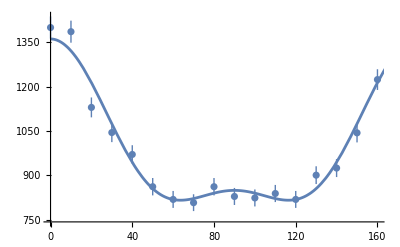

```mathematica
Show[ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData], Plot[a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+a3 f3[Cos[x Degree]],{x,0,200}]]
```

```mathematica
RandomInteger[{-10,10},{3,3}]//MatrixForm
```

(4 | 8 | -1
9 | 3 | 0
-4 | 8 | 6)

```mathematica
Det[({{-2, -5, -6}, {5, 0, -6}, {3, 5, 8}})]+Det[({{5, -5, -6}, {8, 0, -6}, {10, 5, 8}})]
```

610

```mathematica
Det[({{3, -5, -6}, {13, 0, -6}, {13, 5, 8}})]
```

610